# Level Crossing Package

#### Calling the package

```mathematica
Get[NotebookDirectory[]<>"levelcrossing.m"]
```

In general, for any function you can type “?FunctionName” to get the help for that function

## Diagonaling the system

Synopsis

```mathematica
?Diagonalize
```

{Eigenvectors,Eigenenergies} = Diagonalize[ωq,η,ωr,g,g_num,ng,tmax,nmax]
	Takes system parameters and gives properly sorted eigenstates and eigenvectos.
	The qubit is a transmon, and is capacitively (charge-charge) coupled to the resonator.
	The coupling between qubit and resoantor is RWA, or in other words is excitation preserving.

		ωq: Qubit frequency.
		η: Qubit anharmonicity.
		ωr: Resonator frequency.
		g: Coupling strenght between resonator and qubit, defined between |0,1> and |1,0> (|qubit-resonator>).
		g_num: Numerical g. This can be used to reduce the nmax in the system for faster calculations. This way any 'simulation n' in the code would correspond to physical photon number of n(g_num/g)^2
		ng: Background charge of transmon. WARNING: This value should not be of the form k/2. Always use non-excat values such as 0.4999.
		tmax: Maximum number of levels for the transmon. For typical parameters 9-10 is enough. WARNING: This value must be an integer.
		nmax: Maximum number of levels for the resonator. WARNING: This value must be an integer.

		Eigenvectors: A tmax*nmax by tmax*nmax matrix, including the eigenvectors. Each eigenvector is a column in this matrix, hence U|barebasis_element> = |eigenbasis_element>.
		Eigenenergies: A tmax*nmax list (column vector), including the eigenenergies.

	NAVIGATING THE RESULT
		Refer to GetEigen[] and GetBare[] functions manuals to find your desired eigenstate/eigenenergy and compare it to the bare state/energy

## Example:

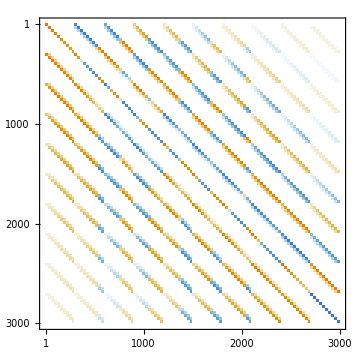
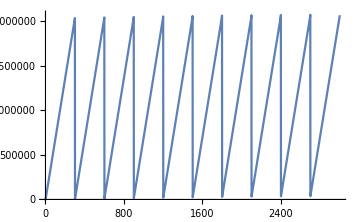

```mathematica
ωq=5441;η=220;ωr=6785;g=90;gnum=200;ng=-0.4999;tmax=10;nmax=300;
{Veigen,Eeigen}=Diagonalize[ωq,η,ωr,g,gnum,ng,tmax,nmax];
{MatrixPlot[Veigen,ImageSize->Medium],ListLinePlot[Eeigen,ImageSize->Medium]}
```

Synopsis

```mathematica
?GetBare
```

{Barestate,Bareenergy}=GetBare[ωq,η,ωr,ng,tmax,nmax,q,n]
	Takes System Parameters and gives the the bare state/energy that belongs to qubit state ''0 <= q <= tmax-1'' and resonator state ''0 <= n <= nmax-1''

		ωq: Qubit frequency.
		η: Qubit anharmonicity.
		ωr: Resonator frequency.
		ng: Background charge of transmon. WARNING: This value should not be of the form k/2. Always use non-excat values such as 0.4999.
		tmax: Maximum number of levels for the transmon. WARNING: This value must be an integer.
		nmax: Maximum number of levels for the resonator. WARNING: This value must be an integer.
		q: The qubit state that you want the eigenvalues for. This must be an integer in the range ''0 <= q <= tmax-1''.
		n: The resonator state that you want the eigenvalues for. This must be an integer in the range ''0 <= n <= nmax-1''.

		Barestate: The bare state belonging to qubit state q and resonator state n.
		Bareenergy: The bare energy belonging to qubit state q and resonator state n.

## Example:

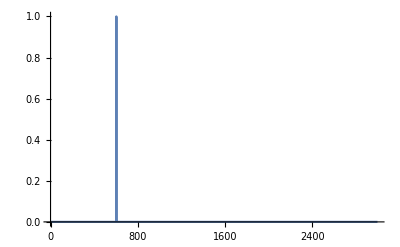

31017.

```mathematica
GetBare[ωq,η,ωr,ng,tmax,nmax,2,3][[1]]//ListLinePlot
GetBare[ωq,η,ωr,ng,tmax,nmax,2,3][[2]]//Normal
```

```mathematica
?GetEigen
```

{Eigenstate,Eigenenergy}=GetEigen[U,E,tmax,nmax,q,n]
	Takes the ORDERED eigenstate and eigenenergies, and gives the the eigenenergy/eigenvector that belongs to qubit state ''0 <= q <= tmax-1'' and resonator state ''0 <= n <= nmax-1''

		U: Ordered matrix including all eigenvectors. Essentially output of Diagonalize.
		E: Ordered list including all eigenvectors. Essentially output of Diagonalize.
		tmax: Maximum number of levels for the transmon. WARNING: This value must be an integer.
		nmax: Maximum number of levels for the resonator. WARNING: This value must be an integer.
		q: The qubit state that you want the eigenvalues for. This must be an integer in the range ''0 <= q <= tmax-1''.
		n: The resonator state that you want the eigenvalues for. This must be an integer in the range ''0 <= n <= nmax-1''.

		Eigenstate: The eigenstate belonging to qubit state q and resonator state n.
		Eigenenergy: The eigenenergy belonging to qubit state q and resonator state n.

## Example:

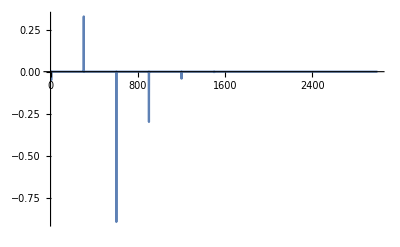

31005.3

```mathematica
GetEigen[Veigen,Eeigen,tmax,nmax,2,3][[1]]//ListLinePlot
GetEigen[Veigen,Eeigen,tmax,nmax,2,3][[2]]//Normal
```

## Processing the Data

Synopsis

```mathematica
?GetFan
```

{E0-vs-n,E1-vs-n,...Etmaxminus1-vs-n}=GetFan[E,tmax,nmax,ωr]
	Takes the ORDERED eigenenergies, and gives the the fan diagram of the system. This means the parameters should be consistent with the ones used in Diagonalize[]

		E: Ordered list including all eigenvectors. Essentially output of Diagonalize.
		tmax: Maximum number of levels for the transmon. WARNING: This value must be an integer.
		nmax: Maximum number of levels for the resonator. WARNING: This value must be an integer.
		ωr: Resonator frequency.

		Eq-vs-n: Energy in the fan diagram versus (simulation) photon number n for qubit q. To convert to physical n, multiply simulation n by (g_num/g)^2

## Example:

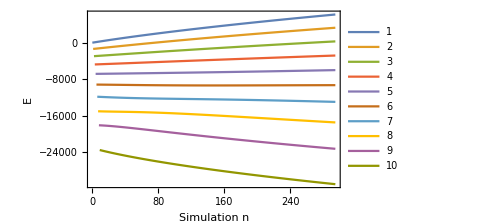
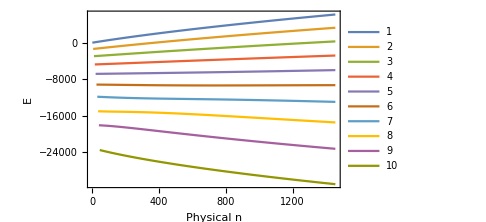
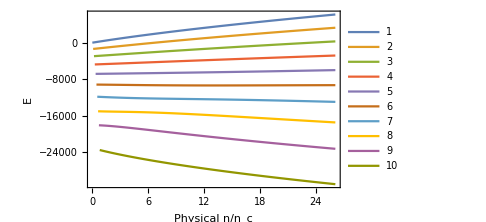
-Graphics- | -Graphics- | -Graphics-

```mathematica
fan=GetFan[Eeigen,tmax,nmax,ωr];
nc=((ωr-ωq)/g)^2/4;
Grid[{{
ListLinePlot[fan,Frame->True,FrameLabel->{"Simulation n","E"},ImageSize->Medium,FrameStyle->13,PlotLegends->Automatic]
,ListLinePlot[{fan[[#]]ᵀ[[1]](gnum/g)^2,fan[[#]]ᵀ[[2]]}ᵀ&/@Range[Length[fan]],Frame->True,FrameLabel->{"Physical n","E"},ImageSize->Medium,FrameStyle->13,PlotLegends->Automatic]
,ListLinePlot[{fan[[#]]ᵀ[[1]](gnum/g)^2/nc,fan[[#]]ᵀ[[2]]}ᵀ&/@Range[Length[fan]],Frame->True,FrameLabel->{"Physical n/n_c","E"},ImageSize->Medium,FrameStyle->13,PlotLegends->Automatic]
}}]
```

Synopsis

```mathematica
?GetCross
```

{n_0,n_1,...,n_tmaxminus1}=GetCross[E,tmax,nmax,ωr,initial_state,resonator_shift]
	Takes the ORDERED eigenenergies, and gives the the fan diagram of the system.

		E: Ordered list including all eigenvectors. Essentially output of Diagonalize.
		tmax: Maximum number of levels for the transmon. WARNING: This value must be an integer.
		nmax: Maximum number of levels for the resonator. WARNING: This value must be an integer.
		ωr: Resonator frequency.
		initial_state: The initial state that you want to find the level crossings from. WARNING: This must be an integer in the range ''0 <= q <= tmax-1''.
		resonator_shift: The number of resonator energies to shift for the level crossing. WARNING: This must be an integer, either 1 or 2.

		n_q: (simulation) photon number n at which there is a crossing between initial_state and the qubit state q. n_q=0 means there is no level crossing. Obviously, always n_q=0 for q<=initial_state.
			To convert to physical n at crossing, multiply n_q by (gnum/g)^2.

## Example

```mathematica
{ncross1=GetCross[Eeigen,tmax,nmax,ωr,0,1],ncross2=GetCross[Eeigen,tmax,nmax,ωr,0,2]}
{GetCross[Eeigen,tmax,nmax,ωr,0,1],GetCross[Eeigen,tmax,nmax,ωr,0,2]}*(gnum/g)^2//Round
```

{{0,0,0,114,0,0,0,0,0,0},{0,0,0,0,0,185,53,0,0,0}}

{{0,0,0,563,0,0,0,0,0,0},{0,0,0,0,0,914,262,0,0,0}}

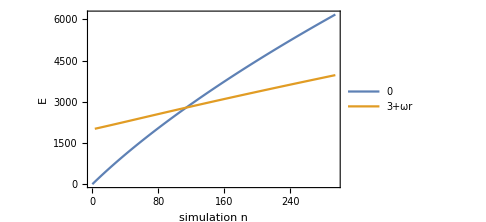
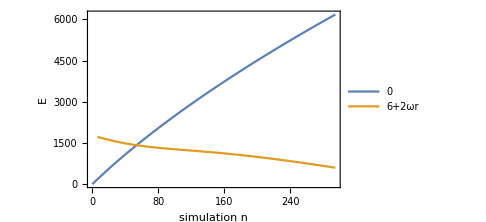
-Graphics- | -Graphics-

```mathematica
Grid[{{init=0;q=3;shift=1;
ListLinePlot[{fan[[init+1]],{fan[[q+1,#,1]],fan[[q+1,#,2]]+(ωr) shift}&/@Range[Length[fan[[q+1]]]]},Frame->True,FrameLabel->{"simulation n","E"},ImageSize->Medium,FrameStyle->13,PlotLegends->{ToString[init],ToString[q]<>"+ωr"},ImageSize->Medium],

init=0;q=6;shift=2;
ListLinePlot[{fan[[init+1]],{fan[[q+1,#,1]],fan[[q+1,#,2]]+(ωr) shift}&/@Range[Length[fan[[q+1]]]]},Frame->True,FrameLabel->{"simulation n","E"},ImageSize->Medium,FrameStyle->13,PlotLegends->{ToString[init],ToString[q]<>"+2ωr"},ImageSize->Medium]
}}]
```

Synopsis

```mathematica
?GetEffg
```

{{coh_geff_0,coh_geff_1,...,coh_geff_tmaxminus1},{incoh_geff_0,incoh_geff_1,...,incoh_geff_tmaxminus1}}=GetCross[Veigen,crossing_list,ωq,η,ωr,g,gnum,ng,tmax,nmax,initial_state,resonator_shift,broken_symmetry]
	Takes the eigenstates and list of n at which crossing happens, gives the effective coupling at the crossing point

		Veigen: The matrix of ordered eigenstates. Essentially the output of Diagonalize[].
		crossing_list: List of n at which crossing happens. This is the output of GetCross[].
		ωq: Qubit frequency.
		η: Qubit anharmonicity.
		ωr: Resonator frequency.
		g: Coupling strenght between resonator and qubit, defined between |0,1> and |1,0> (|qubit-resonator>).
		g_num: Numerical g. This can be used to reduce the nmax in the system for faster calculations. This way any 'simulation n' in the code would correspond to physical photon number of n(g_num/g)^2
		tmax: Maximum number of levels for the transmon. WARNING: This value must be an integer.
		nmax: Maximum number of levels for the resonator. WARNING: This value must be an integer.
		ωr: Resonator frequency.
		initial_state: The initial state that the crossing starts from. This must be an integer in the range ''0 <= q <= tmax-1''.
		resonator_shift: The number of resonator energies to shift for the level crossing. This must be an integer, either 1 or 2.
		broken_symmetry: The breakage of selection rule. The program sets: g_(k, k + 2)=broken_symmetry*√((k + 1) (k + 2)).

		coh_geff_q: Coherent effective coupling normalized by g_num, for corssing between initial_state and qubit state q. Value of 0 means no crossing for that state.
		incoh_geff_q: Incoherent effective coupling normalized by g_num, for corssing between initial_state and qubit state q. Value of 0 means no crossing for that state.

## Example

```mathematica
init=0;shift=1;
GetEffg[Veigen,ncross1,ωq,η,ωr,g,gnum,ng,tmax,nmax,init,shift,0.01]
```

{{0,0,0,0.0693471,0,0,0,0,0,0},{0,0,0,0.106332,0,0,0,0,0,0}}

```mathematica
init=0;shift=2;
GetEffg[Veigen,ncross2,ωq,η,ωr,g,gnum,ng,tmax,nmax,init,shift,0.01]
```

{{0,0,0,0,0,0.337622,0.0287119,0,0,0},{0,0,0,0,0,7.94703,1.3317,0,0,0}}